# , , row=8 , ,

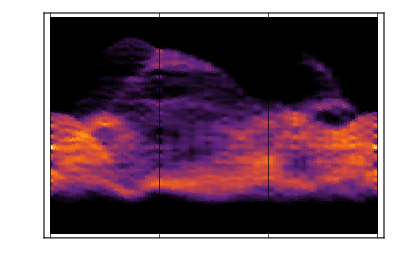

```mathematica
Needs["MaTeX`"]
d1=d1=Import["dsf8a.dat","Table"];
n=40;mag=2.0;marg=0;
(*autoYTicks[range_]:=Module[{ticks,positions,labels},positions=Subdivide[range[[1]],range[[2]],2];labels=NumberForm[#,{Infinity,1}]&/@positions;ticks=Transpose[{positions,labels}];ticks];*)
autoYTicks[range_]:=Module[{ticks,positions,labels},positions=Subdivide[range[[1]],range[[2]],2];
labels=MaTeX[NumberForm[#,{Infinity,1}],Magnification->mag]&/@positions;
ticks=Transpose[{positions,labels}];ticks];

colorF=(ColorData["SunsetColors"][Rescale[#,{0.10,1.0}]]&);plotRange={{1,3 n+1},Full,Full};frameStyle=Directive[Black,FontFamily->"Latin Modern Roman"];
gridL={{1,n+1,2 n+1,3 n+1,4 n+1,5 n+1},None};gridLstyle=Directive[Black];
xTicks={{1,MaTeX["\\Gamma",Magnification->mag]},{n+1,MaTeX["M'",Magnification->mag]},{2 n+1,MaTeX["K'",Magnification->mag]},{3 n+1,MaTeX["\\Gamma",Magnification->mag]}};

p1=With[{l=d1},ListDensityPlot[l,Frame->True,FrameStyle->frameStyle;ColorFunction->colorF,ColorFunctionScaling->True,PlotRange->plotRange,GridLines->gridL,GridLinesStyle->gridLstyle,FrameTicks->{{autoYTicks[{Min[l[[All,2]]],Max[l[[All,2]]]*0.95}],None},{xTicks,None}},AspectRatio->0.65]]
```